## Equation:

```mathematica
h[x_,t_]:= Log[ Cos[x+β t]]+α t^2
```

```mathematica
h[x_,t_]:= Log[ x+β t]+α t^2
```

```mathematica
Eq = D[h[τ,x], τ,τ] +A(D[h[τ,x], x] )^2+ B D[h[τ,x], x,x]
```

-Sec[x β+τ]^2+B (2 α-β^2 Sec[x β+τ]^2)+A (2 x α-β Tan[x β+τ])^2

```mathematica
Sols = Solve[Eq ==0,{α,β}]
```

{{α→(-2 B+40)/(2 A x^2 (4-8 Cos[τ]^2+16 Cos[x β]^2 Cos[τ]^2+12+4 Sin[τ]^4-16 Cos[x β]^2 Sin[τ]^4+16 Cos[x β]^4 Sin[τ]^4))},{α→1/1},4,{α→1},{α→(-2 B+38+√(-4 A x^2 (1) (-2+33)+1^2))/(2 A x^2 (4-8 1^2+16+16 Cos[x β]^4 Sin[τ]^4))}}
 |  |  |  |

```mathematica
Sols = Solve[Eq ==0/.α->1,{β}]
```

{{β→-1/(√(A-B))},{β→1/(√(A-B))}}

#### Solutions symbolic

```mathematica
Sol1 = ComplexExpand[h[x,t]/.Sols[[1]]]
```

ⅈ α Arg[-t/(√(A-B))+x]+α Log[√((x-(t Cos[1/2 Arg[A-B]])/(((A-B)^2)^(1/4)))^2+(t^2 Sin[1/2 Arg[A-B]]^2)/(√((A-B)^2)))]

```mathematica
Sol2 = ComplexExpand[h[x,t]/.Sols[[2]]]
```

ⅈ α Arg[t/(√(A-B))+x]+α Log[√((x+(t Cos[1/2 Arg[A-B]])/(((A-B)^2)^(1/4)))^2+(t^2 Sin[1/2 Arg[A-B]]^2)/(√((A-B)^2)))]

## Different limits

#### Limit of A to 0 and finite positive B (We expect to be a complex wave equation!)[Here it only blows up at t=0,x=0]

```mathematica
DSolve[ D[g[τ,x], τ,τ] +D[g[τ,x], x,x] ==0,g[τ,x],τ,x]
```

{{g[τ,x]→C[1][x+ⅈ τ]+C[2][x-ⅈ τ]}}

```mathematica
Im[Sol1/.A->0/.B->1]
```

Im[α Log[√(t^2+x^2)]]+Re[α Arg[ⅈ t+x]]

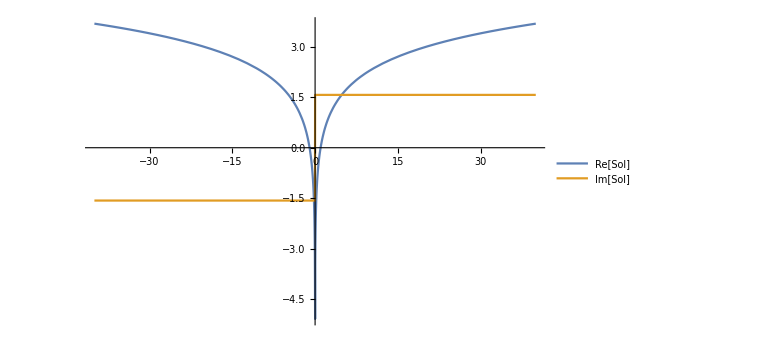

```mathematica
Plot[{Re[Sol1/.α->1/.A->0/.B->1/.x->0],Im[Sol1/.α->1/.A->0/.B->1/.x->0]},{t,-40,40},PlotLegends->{"Re[Sol]","Im[Sol]"},ImageSize->Large]
```

Second solution:

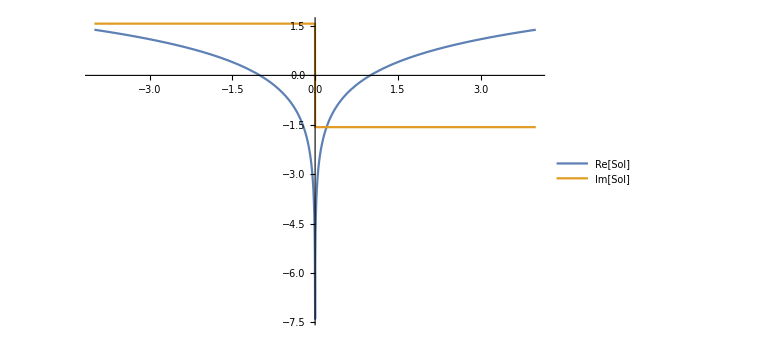

```mathematica
Plot[{Re[Sol2/.α->1/.A->0/.B->1/.x->0],Im[Sol2/.α->1/.A->0/.B->1/.x->0]},{t,-4,4},PlotLegends->{"Re[Sol]","Im[Sol]"},ImageSize->Large]
```

#### Limit of A to 0 and finite negative B (We expect to be a wave equation!) [Here it only blows up at t=0,x=0]

```mathematica
DSolve[ D[g[τ,x], τ,τ] -D[g[τ,x], x,x] ==0,g[τ,x],τ,x]
```

{{g[τ,x]→C[1][x-τ]+C[2][x+τ]}}

```mathematica
Im[Sol1/.A->0/.B->-1]
```

Im[α Log[√((-t+x)^2)]]+Re[α Arg[-t+x]]

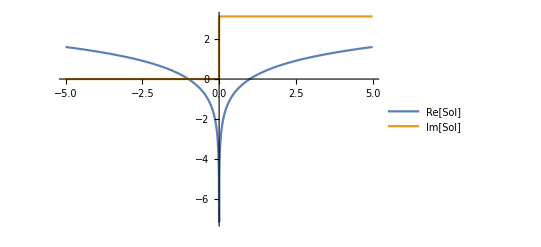

```mathematica
Plot[{Re[Sol1/.α->1/.A->0/.B->-1/.x->0],Im[Sol1/.α->1/.A->0/.B->-1/.x->0]},{t,-5,5},PlotLegends->{"Re[Sol]","Im[Sol]"}]
```

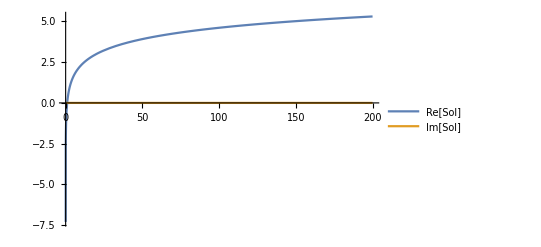

```mathematica
Plot[{Re[Sol2/.α->1/.A->0/.B->-1/.x->0],Im[Sol2/.α->1/.A->0/.B->-1/.x->0]},{t,0,200},PlotLegends->{"Re[Sol]","Im[Sol]"}]
```

#### Limit of B to 0 and finite pm A (We expect to see the blowup solution!) [It always blow up for any x]

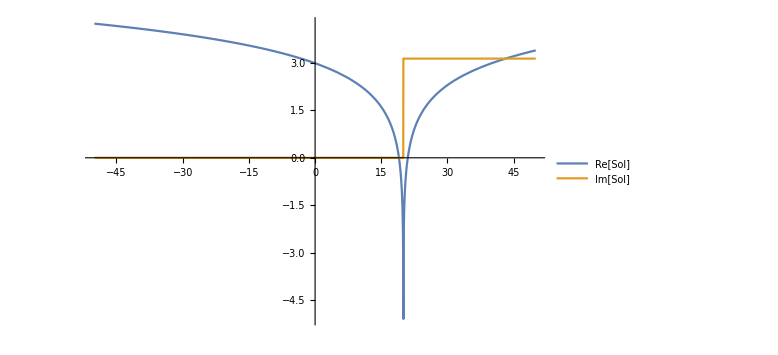

```mathematica
Plot[{Re[Sol1/.α->1/.A->1/.B->0/.x->20],Im[Sol1/.α->1/.A->1/.B->0/.x->20]},{t,-50,50},PlotLegends->{"Re[Sol]","Im[Sol]"},ImageSize->Large]
```

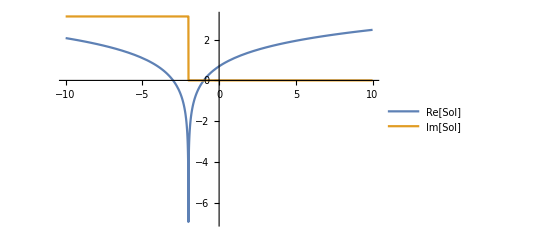

```mathematica
Plot[{Re[Sol2/.α->1/.A->1/.B->0/.x->2],Im[Sol2/.α->1/.A->1/.B->0/.x->2]},{t,-10,10},PlotLegends->{"Re[Sol]","Im[Sol]"}](*It blows up at negative times, for positive x*)
```

#### Some tests:

WolframAlphaQueryResults